## Expand the exact Mellin in collinear limit

### Expand in ξ ->

```mathematica
Series[(√(ξ + 1) - √ξ)^4, {ξ, 0, 1}]
```

1-4 √ξ+8 ξ+O[ξ]^(3/2)

```mathematica
(* Expand in δ -> 0 *)
```

```mathematica
Series[(1 - a^2)^-δ,  {δ, 0, 1}]
```

1-Log[1-a^2] δ+O[δ]^2

```mathematica
Series[(Gamma[n + 1/2]Gamma[δ])/(Gamma[1/2 + δ]Gamma[n]), {δ, 0, 0}] // FunctionExpand // FullSimplify
```

Gamma[1/2+n]/(√π Gamma[n] δ)+(Gamma[1/2+n] Log[4])/(√π Gamma[n])+O[δ]^1

```mathematica
Series[(Gamma[n + 1/2]Gamma[-δ])/(Gamma[n - δ]Gamma[1/2]), {δ, 0, 0}] // FunctionExpand // FullSimplify
```

-Gamma[1/2+n]/(√π Gamma[n] δ)-(Gamma[1/2+n] (EulerGamma+PolyGamma[0,n]))/(√π Gamma[n])+O[δ]^1

### Shift to terms of the form Log(1 - zmax2)

```mathematica
(* Express everyting in zmax = (√(ξ + 1) - √ξ)^2 *)
(* Logs of (1 - zmax^2) may contain more information that pure logs of ξ *)
```

```mathematica
Series[(4z)^(1+ϵ), {z, 1, 1}]
```

4^(1+ϵ)+4^(1+ϵ) (1+ϵ) (z-1)+O[z-1]^2

```mathematica
Series[(1 - z)^α, {z, 1, 1}]
```

(1-z)^α

```mathematica
Series[Log[1 - z^2], {z, 1, 1}, Assumptions -> Element[z, Reals] && a > 0]
```

Log[-2 (-1+z)]+(z-1)/2+O[z-1]^2

```mathematica
(* Expansions in δ and z do commute *)
```

```mathematica
expz = FullSimplify[Series[(4z)^(1+ϵ)(1 - z)^(-2-2ϵ)Beta[n, 1/2]((1 - z^2)^-δ(Gamma[n + 1/2]Gamma[δ])/(Gamma[1/2 + δ]Gamma[n]) + (Gamma[n + 1/2]Gamma[-δ])/(Gamma[n - δ]Gamma[1/2])), {δ, 0, 0}]]
```

-4^(1+ϵ) (1-z)^(-2 (1+ϵ)) z^(1+ϵ) (EulerGamma+Log[1/4 (1-z^2)]+PolyGamma[0,n])+O[δ]^1

```mathematica
expz2 = Series[expz, {z, 1, 0}, Assumptions -> Element[z, Reals] && a > 0]
```

(1-z)^(-2 (1+ϵ)) (-4^(1+ϵ) (EulerGamma-Log[2]+Log[1-z]+PolyGamma[0,n])+O[z-1]^1)+O[δ]^1

```mathematica
(* Expand finally in ϵ *)
```

```mathematica
expa3 = Series[expa, {ϵ, 0, 0}, Assumptions -> Element[a, Reals] && a > 0]
```

(-(4 (z (EulerGamma+Log[1/4 (1-z^2)]+PolyGamma[0,n])))/(-1+z)^2+O[ϵ]^1)+O[δ]^1

## Low ξ limit (collinear)

```mathematica
(* Exact Mellin transformed *)
```

```mathematica
Clear[n]
Clear[ξ]
```

```mathematica
exact = 1/ξ Beta[n, 1/2]Hypergeometric2F1[1/2 , n, n + 1/2, a2]
```

(Beta[n,1/2] Hypergeometric2F1[1/2,n,1/2+n,a2])/ξ

```mathematica
(* Collinear limit - known by resummation *)
```

```mathematica
collinear= -1/2 Log[ξ]/ξ - 1/ξ(PolyGamma[0, n] + EulerGamma)
```

-Log[ξ]/(2 ξ)-(EulerGamma+PolyGamma[0,n])/ξ

```mathematica
collinear2 = 1/ξ(Log[4] - Log[1 - (√(ξ + 1) - √ξ)^4] - (PolyGamma[0, n] + EulerGamma))
```

(-EulerGamma+Log[4]-Log[1-(-√ξ+√(1+ξ))^4]-PolyGamma[0,n])/ξ

```mathematica
table1 = Table[{ξ,collinear /. n -> 100}, {ξ, 0.01, 1, 0.001}];
table2 = Table[{ξ, exact /. {n -> 100, a2 -> (√(ξ + 1) - √ξ)^4} }, {ξ, 0.01, 1, 0.001}];
```

```mathematica
ListPlot[{table1, table2}, PlotLegends -> {"Collinear expanded N = 100", "Exact N = 100"}];
```

```mathematica
(* Extend the range to observe the convergence - log scale *)
(* From 10^-5 to 10^-9 the sign of the collinear should change and diverge at +∞ *)
```

```mathematica
collinearsmallpt = Table[Table[{lnξ, collinear} /. {ξ -> 10^lnξ}, {lnξ, -9, -1, 0.01}], {n, {2, 100}}];
exactsmallpt = Table[Table[{lnξ,exact } //. {a2 -> (√(ξ + 1) - √ξ)^4, ξ -> 10^lnξ}, {lnξ, -9, -1, 0.01}], {n, {2, 100}}];
```

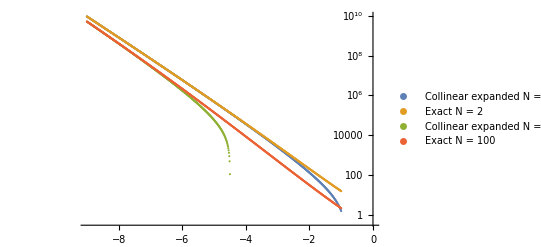

```mathematica
ListLogPlot[{collinearsmallpt[[1]], exactsmallpt[[1]], collinearsmallpt[[2]], exactsmallpt[[2]]},PlotLegends -> {"Collinear expanded N = 2", "Exact N = 2","Collinear expanded N = 100", "Exact N = 100"}]
```

```mathematica
ratioCollinear = collinear/exact
```

(ξ (-Log[ξ]/(2 ξ)-(EulerGamma+PolyGamma[0,n])/ξ))/(Beta[n,1/2] Hypergeometric2F1[1/2,n,1/2+n,a2])

```mathematica
tableRatio = Table[{lnξ, ratioCollinear //. {n -> 2, a2 -> (√(ξ + 1) - √ξ)^4,  ξ -> 10^lnξ }} , {lnξ, -15, -5, 0.1}];
```

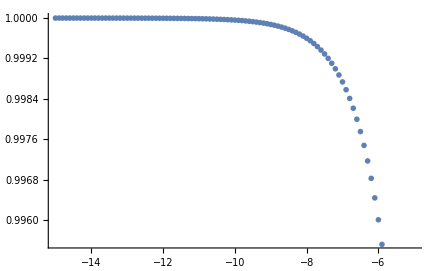

```mathematica
ListPlot[tableRatio]
```

## Large ξ limit

```mathematica
Series[Hypergeometric2F1[1/2 , n, n + 1/2, a2] /. a2 -> (√(ξ + 1) - √ξ)^4, {ξ, ∞,1}]
```

1+O[1/ξ]^(3/2)

```mathematica
largept = Normal[Series[1/ξ Beta[n, 1/2]Hypergeometric2F1[1/2 , n, n + 1/2, a2] /. a2 -> (√(ξ + 1) - √ξ)^4, {ξ, ∞, 1}]]
```

Beta[n,1/2]/ξ

```mathematica
n = 10;
```

```mathematica
tableLargept = Table[{lnξ, largept} /. ξ -> 10^lnξ, {lnξ, -7,2,.1}]
tableLowpt = Table[{lnξ, collinear} /. ξ -> 10^lnξ,  {lnξ, -7,2,.1}]
tableLowpt2 = Table[{lnξ, collinear2} /. ξ -> 10^lnξ,  {lnξ, -7,2,.1}]
tableExactpt= Table[{lnξ,1/ξ Beta[n, 1/2]Hypergeometric2F1[1/2 , n, n + 1/2, a2]} //. {a2 -> (√(ξ + 1) - √ξ)^4 , ξ -> 10^lnξ}, {lnξ, -7,2,.1}]
```

{{-7.,5.67546×10^6},{-6.9,4.50818×10^6},{-6.8,3.58098×10^6},{-6.7,2.84447×10^6},{-6.6,2.25944×10^6},{-6.5,1.79474×10^6},{-6.4,1.42561×10^6},{-6.3,1.1324×10^6},{-6.2,899500.},{-6.1,714499.},{-6.,567546.},{-5.9,450818.},{-5.8,358098.},{-5.7,284447.},{-5.6,225944.},{-5.5,179474.},{-5.4,142561.},{-5.3,113240.},{-5.2,89950.},{-5.1,71449.9},{-5.,56754.6},{-4.9,45081.8},{-4.8,35809.8},{-4.7,28444.7},{-4.6,22594.4},{-4.5,17947.4},{-4.4,14256.1},{-4.3,11324.},{-4.2,8995.},{-4.1,7144.99},{-4.,5675.46},{-3.9,4508.18},{-3.8,3580.98},{-3.7,2844.47},{-3.6,2259.44},{-3.5,1794.74},{-3.4,1425.61},{-3.3,1132.4},{-3.2,899.5},{-3.1,714.499},{-3.,567.546},{-2.9,450.818},{-2.8,358.098},{-2.7,284.447},{-2.6,225.944},{-2.5,179.474},{-2.4,142.561},{-2.3,113.24},{-2.2,89.95},{-2.1,71.4499},{-2.,56.7546},{-1.9,45.0818},{-1.8,35.8098},{-1.7,28.4447},{-1.6,22.5944},{-1.5,17.9474},{-1.4,14.2561},{-1.3,11.324},{-1.2,8.995},{-1.1,7.14499},{-1.,5.67546},{-0.9,4.50818},{-0.8,3.58098},{-0.7,2.84447},{-0.6,2.25944},{-0.5,1.79474},{-0.4,1.42561},{-0.3,1.1324},{-0.2,0.8995},{-0.1,0.714499},{0.,0.567546},{0.1,0.450818},{0.2,0.358098},{0.3,0.284447},{0.4,0.225944},{0.5,0.179474},{0.6,0.142561},{0.7,0.11324},{0.8,0.08995},{0.9,0.0714499},{1.,0.0567546},{1.1,0.0450818},{1.2,0.0358098},{1.3,0.0284447},{1.4,0.0225944},{1.5,0.0179474},{1.6,0.0142561},{1.7,0.011324},{1.8,0.008995},{1.9,0.00714499},{2.,0.00567546}}

{{-7.,5.23008×10^7},{-6.9,4.06295×10^7},{-6.8,3.15467×10^7},{-6.7,2.44815×10^7},{-6.6,1.8988×10^7},{-6.5,1.47186×10^7},{-6.4,1.14022×10^7},{-6.3,8.82739×10^6},{-6.2,6.82938×10^6},{-6.1,5.27983×10^6},{-6.,4.07879×10^6},{-5.9,3.14845×10^6},{-5.8,2.42826×10^6},{-5.7,1.87113×10^6},{-5.6,1.44046×10^6},{-5.5,1.10779×10^6},{-5.4,851030.},{-5.3,653026.},{-5.2,500470.},{-5.1,383044.},{-5.,292749.},{-4.9,223394.},{-4.8,170184.},{-4.7,129412.},{-4.6,98212.1},{-4.5,74372.},{-4.4,56183.8},{-4.3,42331.3},{-4.2,31800.3},{-4.1,23810.4},{-4.,17762.},{-3.9,13194.4},{-3.8,9754.24},{-3.7,7171.06},{-3.6,5237.84},{-3.5,3796.49},{-3.4,2726.47},{-3.3,1936.},{-3.2,1355.35},{-3.1,931.653},{-3.,624.909},{-2.9,404.933},{-2.8,249.008},{-2.7,140.093},{-2.6,65.4458},{-2.5,15.5784},{-2.4,-16.5448},{-2.3,-36.1133},{-2.2,-46.9326},{-2.1,-51.7738},{-2.,-52.6383},{-1.9,-50.9571},{-1.8,-47.7409},{-1.7,-43.692},{-1.6,-39.2892},{-1.5,-34.8492},{-1.4,-30.5736},{-1.3,-26.5826},{-1.2,-22.94},{-1.1,-19.6713},{-1.,-16.7768},{-0.9,-14.2408},{-0.8,-12.0383},{-0.7,-10.1393},{-0.6,-8.5123},{-0.5,-7.12563},{-0.4,-5.94928},{-0.3,-4.95539},{-0.2,-4.11868},{-0.1,-3.41652},{0.,-2.82897},{0.1,-2.33858},{0.2,-1.93024},{0.3,-1.59095},{0.4,-1.30957},{0.5,-1.07663},{0.6,-0.88412},{0.7,-0.725253},{0.8,-0.594335},{0.9,-0.486591},{1.,-0.398026},{1.1,-0.325308},{1.2,-0.265666},{1.3,-0.216796},{1.4,-0.176791},{1.5,-0.14407},{1.6,-0.117331},{1.7,-0.0954966},{1.8,-0.0776803},{1.9,-0.063153},{2.,-0.0513155}}

{{-7.,5.23071×10^7},{-6.9,4.06351×10^7},{-6.8,3.15518×10^7},{-6.7,2.44859×10^7},{-6.6,1.8992×10^7},{-6.5,1.47222×10^7},{-6.4,1.14054×10^7},{-6.3,8.83021×10^6},{-6.2,6.83189×10^6},{-6.1,5.28207×10^6},{-6.,4.08079×10^6},{-5.9,3.15023×10^6},{-5.8,2.42985×10^6},{-5.7,1.87255×10^6},{-5.6,1.44172×10^6},{-5.5,1.10891×10^6},{-5.4,852032.},{-5.3,653919.},{-5.2,501266.},{-5.1,383753.},{-5.,293381.},{-4.9,223957.},{-4.8,170686.},{-4.7,129859.},{-4.6,98610.7},{-4.5,74727.1},{-4.4,56500.3},{-4.3,42613.3},{-4.2,32051.5},{-4.1,24034.3},{-4.,17961.5},{-3.9,13372.1},{-3.8,9912.61},{-3.7,7312.14},{-3.6,5363.52},{-3.5,3908.45},{-3.4,2826.2},{-3.3,2024.83},{-3.2,1434.46},{-3.1,1002.11},{-3.,687.645},{-2.9,460.789},{-2.8,298.733},{-2.7,184.353},{-2.6,104.835},{-2.5,50.626},{-2.4,14.633},{-2.3,-8.38487},{-2.2,-22.2789},{-2.1,-29.8611},{-2.,-33.169},{-1.9,-33.6662},{-1.8,-32.392},{-1.7,-30.0749},{-1.6,-27.2161},{-1.5,-24.1531},{-1.4,-21.1055},{-1.3,-18.2098},{-1.2,-15.5442},{-1.1,-13.1469},{-1.,-11.0297},{-0.9,-9.18697},{-0.8,-7.60265},{-0.7,-6.25472},{-0.6,-5.11844},{-0.5,-4.16844},{-0.4,-3.38008},{-0.3,-2.73028},{-0.2,-2.19797},{-0.1,-1.76433},{0.,-1.41279},{0.1,-1.12905},{0.2,-0.900853},{0.3,-0.717889},{0.4,-0.571548},{0.5,-0.454723},{0.6,-0.361595},{0.7,-0.287439},{0.8,-0.228434},{0.9,-0.181511},{1.,-0.144211},{1.1,-0.114567},{1.2,-0.0910118},{1.3,-0.0722975},{1.4,-0.0574301},{1.5,-0.0456194},{1.6,-0.0362374},{1.7,-0.0287846},{1.8,-0.0228646},{1.9,-0.0181621},{2.,-0.0144267}}

{{-7.,5.26332×10^7},{-6.9,4.09194×10^7},{-6.8,3.17995×10^7},{-6.7,2.47017×10^7},{-6.6,1.91798×10^7},{-6.5,1.48856×10^7},{-6.4,1.15475×10^7},{-6.3,8.95376×10^6},{-6.2,6.93922×10^6},{-6.1,5.37526×10^6},{-6.,4.16165×10^6},{-5.9,3.22035×10^6},{-5.8,2.49062×10^6},{-5.7,1.92519×10^6},{-5.6,1.48728×10^6},{-5.5,1.14832×10^6},{-5.4,886089.},{-5.3,683332.},{-5.2,526649.},{-5.1,405641.},{-5.,312240.},{-4.9,240192.},{-4.8,184649.},{-4.7,141858.},{-4.6,108913.},{-4.5,83563.3},{-4.4,64071.9},{-4.3,49094.6},{-4.2,37593.8},{-4.1,28768.6},{-4.,22001.1},{-3.9,16815.},{-3.8,12843.6},{-3.7,9804.38},{-3.6,7480.08},{-3.5,5703.72},{-3.4,4347.},{-3.3,3311.43},{-3.2,2521.48},{-3.1,1919.24},{-3.,1460.36},{-2.9,1110.89},{-2.8,844.882},{-2.7,642.482},{-2.6,488.543},{-2.5,371.5},{-2.4,282.533},{-2.3,214.921},{-2.2,163.545},{-2.1,124.507},{-2.,94.8431},{-1.9,72.299},{-1.8,55.1616},{-1.7,42.1295},{-1.6,32.2144},{-1.5,24.6661},{-1.4,18.9152},{-1.3,14.5297},{-1.2,11.1818},{-1.1,8.62273},{-1.,6.66379},{-0.9,5.16173},{-0.8,4.00785},{-0.7,3.11958},{-0.6,2.4342},{-0.5,1.90406},{-0.4,1.49289},{-0.3,1.17312},{-0.2,0.923714},{-0.1,0.728649},{0.,0.575674},{0.1,0.455409},{0.2,0.36065},{0.3,0.285845},{0.4,0.2267},{0.5,0.179877},{0.6,0.142774},{0.7,0.113352},{0.8,0.090008},{0.9,0.0714798},{1.,0.05677},{1.1,0.0450897},{1.2,0.0358137},{1.3,0.0284467},{1.4,0.0225955},{1.5,0.0179479},{1.6,0.0142564},{1.7,0.0113242},{1.8,0.00899507},{1.9,0.00714502},{2.,0.00567548}}

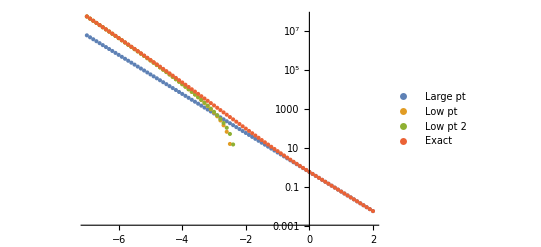

```mathematica
ListLogPlot[{tableLargept,tableLowpt,tableLowpt2, tableExactpt},PlotLegends->{"Large pt", "Low pt", "Low pt 2", "Exact"}]
```

```mathematica
Fit[Table[{lnξ,1/ξ Beta[n, 1/2]Hypergeometric2F1[1/2 , n, n + 1/2, a2] }//. {a2 -> (√(ξ + 1) - √ξ)^2 , ξ -> 10^lnξ}, {lnξ, -7,1,.1}],{1,ln,ln^2},ln]
```

602158.+4.4507×10^6 ln+1.1099×10^6 ln^2

```mathematica
(* Numerical integration with cut ξ = 0.1 *)
```

```mathematica
function = 1/x Beta[x, 1/2]Hypergeometric2F1[1/2 , 2, 2 + 1/2, (√(x+1) - √x)^4]
```

(Beta[x,1/2] Hypergeometric2F1[1/2,2,5/2,(-√x+√(1+x))^4])/x

```mathematica
integrated = NIntegrate[function, {x, 0.1, 1000000000000000}]
```

16.3856

## Large N limit (threshold)

```mathematica
Clear[n]
Clear[ξ]
```

```mathematica
exactN= 1/ξ Beta[n, 1/2]Hypergeometric2F1[1/2 , n, n + 1/2, a2] /. a2 -> (√(ξ + 1) - √ξ)^4
```

(Beta[n,1/2] Hypergeometric2F1[1/2,n,1/2+n,(-√ξ+√(1+ξ))^4])/ξ

```mathematica
Series[Beta[n, 1/2], {n, ∞, 1}]
```

√π √(1/n)+O[1/n]^(3/2)

```mathematica
(* Solve hypergeometric equation in large N limit to determine 2F1 behavior *)
```

```mathematica
DSolve[(1 - z)u'[z] - u[z]/2 == 0, u[z], z]
```

{{u[z]→C[1]/(√(2-2 z))}}

```mathematica
largeN = 1/ξ(√π)/(√(n(1 - a2))) /. a2 -> (√(ξ + 1) - √ξ)^4
```

(√π)/(ξ √(n (1-(-√ξ+√(1+ξ))^4)))

```mathematica
(* Maybe better approx to write the beta function instead of the expansion at large n *)
(* In a similar way we did writinng polygamma than lnN *)
```

```mathematica
tableLargeN= Table[Table[{n, largeN}, {n, 0.1, 10, 0.1}], {ξ, {0.5, 1, 10}}];
tableExactN= Table[Table[{n, exactN}, {n, 0.1, 10, 0.1}], {ξ, {0.5, 1, 10}}];
```

```mathematica
(* Plot exact expression and low N expanded vs N at fixed ξ *)
```

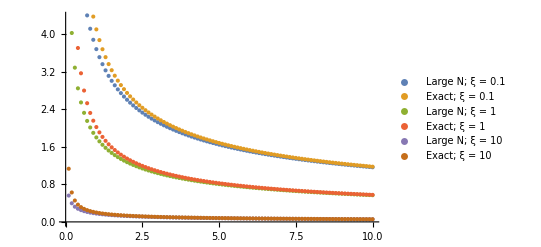

```mathematica
ListPlot[{tableLargeN[[1]], tableExactN[[1]], tableLargeN[[2]], tableExactN[[2]], tableLargeN[[3]], tableExactN[[3]]}, PlotLegends -> {"Large N; ξ = 0.1", "Exact; ξ = 0.1", "Large N; ξ = 1", "Exact; ξ = 1", "Large N; ξ = 10", "Exact; ξ = 10"}]
```

```mathematica
ratioLargeN = tableLargeN / tableExactN;
ratioLargeN1 = ratioLargeN[[1]][[All,2]]
ratioLargeN2 = ratioLargeN[[2]][[All,2]]
ratioLargeN3 = ratioLargeN[[3]][[All,2]]
```

{0.510619,0.649316,0.727301,0.77772,0.812956,0.838901,0.858752,0.874397,0.887022,0.897411,0.906099,0.913466,0.919786,0.925266,0.930059,0.934286,0.93804,0.941395,0.944411,0.947136,0.94961,0.951865,0.95393,0.955827,0.957575,0.959192,0.960691,0.962085,0.963384,0.964598,0.965735,0.966801,0.967804,0.968748,0.969639,0.97048,0.971277,0.972032,0.972748,0.973429,0.974077,0.974694,0.975283,0.975845,0.976382,0.976896,0.977388,0.977859,0.978312,0.978746,0.979164,0.979565,0.979951,0.980323,0.980681,0.981027,0.981361,0.981683,0.981994,0.982295,0.982586,0.982867,0.98314,0.983404,0.98366,0.983908,0.984149,0.984382,0.984609,0.98483,0.985044,0.985252,0.985455,0.985652,0.985844,0.986031,0.986213,0.98639,0.986563,0.986731,0.986895,0.987056,0.987212,0.987365,0.987514,0.987659,0.987801,0.98794,0.988076,0.988209,0.988339,0.988466,0.988591,0.988712,0.988831,0.988948,0.989062,0.989174,0.989284,0.989391}

{0.501208,0.639032,0.717196,0.768093,0.803878,0.830367,0.850729,0.866842,0.879894,0.890669,0.899708,0.907393,0.914004,0.919748,0.924785,0.929234,0.933193,0.936738,0.93993,0.942818,0.945443,0.947841,0.950038,0.952059,0.953924,0.95565,0.957252,0.958744,0.960135,0.961436,0.962655,0.9638,0.964877,0.965893,0.966851,0.967757,0.968615,0.969429,0.970202,0.970937,0.971636,0.972303,0.972939,0.973547,0.974128,0.974684,0.975217,0.975728,0.976219,0.97669,0.977142,0.977578,0.977997,0.978401,0.97879,0.979166,0.979528,0.979879,0.980217,0.980544,0.980861,0.981167,0.981464,0.981752,0.982031,0.982301,0.982564,0.982818,0.983066,0.983306,0.98354,0.983767,0.983988,0.984204,0.984413,0.984617,0.984816,0.985009,0.985198,0.985382,0.985562,0.985737,0.985908,0.986075,0.986238,0.986397,0.986553,0.986705,0.986854,0.986999,0.987142,0.987281,0.987417,0.98755,0.987681,0.987809,0.987934,0.988057,0.988177,0.988295}

{0.495123,0.632374,0.710651,0.761855,0.797998,0.824841,0.845535,0.861954,0.875283,0.886311,0.895578,0.903471,0.910272,0.916189,0.921383,0.925978,0.930071,0.933739,0.937045,0.940039,0.942763,0.945253,0.947536,0.949637,0.951578,0.953375,0.955045,0.956599,0.95805,0.959408,0.96068,0.961876,0.963002,0.964063,0.965065,0.966013,0.966911,0.967762,0.968572,0.969341,0.970074,0.970773,0.97144,0.972077,0.972687,0.97327,0.97383,0.974366,0.974881,0.975375,0.975851,0.976308,0.976749,0.977173,0.977582,0.977977,0.978359,0.978727,0.979083,0.979427,0.97976,0.980083,0.980395,0.980698,0.980991,0.981276,0.981552,0.981821,0.982081,0.982335,0.982581,0.98282,0.983053,0.98328,0.983501,0.983716,0.983925,0.98413,0.984329,0.984523,0.984712,0.984897,0.985077,0.985254,0.985426,0.985594,0.985758,0.985918,0.986075,0.986229,0.986379,0.986526,0.98667,0.98681,0.986948,0.987083,0.987215,0.987345,0.987472,0.987596}

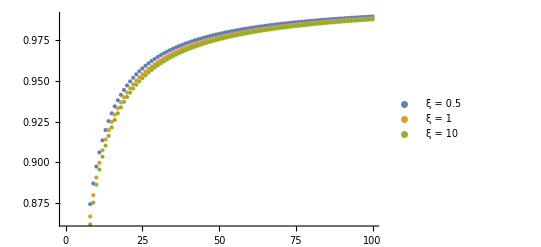

```mathematica
ListPlot[{ratioLargeN1, ratioLargeN2, ratioLargeN3}, PlotLegends -> {"ξ = 0.5", "ξ = 1", "ξ = 10"}]
```

## Low N limit

```mathematica
Clear[n]
Clear[ξ]
```

```mathematica
exactN= 1/ξ Beta[n, 1/2]Hypergeometric2F1[1/2 , n, n + 1/2, a2] /. a2 -> (√(ξ + 1) - √ξ)^4
```

(Beta[n,1/2] Hypergeometric2F1[1/2,n,1/2+n,(-√ξ+√(1+ξ))^4])/ξ

```mathematica
(* 1. Expand in δ -> 0 *)
```

```mathematica
Series[Hypergeometric2F1[n - δ, 1/2, 1 - δ, 1 - a2], {δ, 0, 1}]
```

Hypergeometric2F1[1/2,n,1,1-a2]+(-Hypergeometric2F1^(0,0,1,0)[1/2,n,1,1-a2]-Hypergeometric2F1^(0,1,0,0)[1/2,n,1,1-a2]) δ+O[δ]^2

```mathematica
Series[Hypergeometric2F1[1/2 - δ, n, 1 + δ, 1 - a2], {δ, 0, 1}]
```

Hypergeometric2F1[1/2,n,1,1-a2]+(Hypergeometric2F1^(0,0,1,0)[n,1/2,1,1-a2]-Hypergeometric2F1^(0,1,0,0)[n,1/2,1,1-a2]) δ+O[δ]^2

```mathematica
(* 2. Expand n -> 0 *)
```

```mathematica
Series[Beta[n, 1/2], {n, 0, 1}]
```

1/n+(-EulerGamma-PolyGamma[0,1/2])+1/6 (3 EulerGamma^2-π^2+6 EulerGamma PolyGamma[0,1/2]+3 PolyGamma[0,1/2]^2) n+O[n]^2

```mathematica
Series[PolyGamma[n], {n, 0, 1}]
```

-1/n-EulerGamma+(π^2 n)/6+O[n]^2

```mathematica
lowN = FullSimplify[Normal[Series[exactN, {n, 0, -1}]]]
```

1/(n ξ)

```mathematica
tableLowN = Table[Table[{lnn, lowN} /. n -> 10^lnn, {lnn, -3, 1, 0.01}], {ξ, {0.1, 1, 10}}];
```

```mathematica
tableExactN2 = Table[Table[{lnn, exactN} /. n -> 10^lnn, {lnn, -3, 1, 0.01}], {ξ, {0.1, 1, 10}}];
```

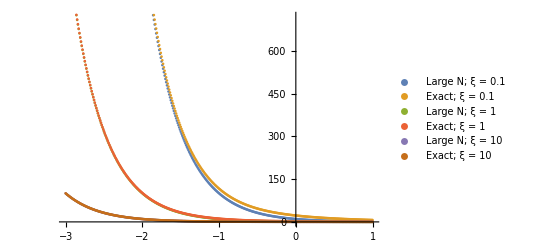

```mathematica
ListPlot[{tableLowN[[1]], tableExactN2[[1]], tableLowN[[2]], tableExactN2[[2]], tableLowN[[3]], tableExactN2[[3]]}, PlotLegends -> {"Large N; ξ = 0.1","Exact; ξ = 0.1", "Large N; ξ = 1","Exact; ξ = 1", "Large N; ξ = 10","Exact; ξ = 10"}]
```

```mathematica
ratioLowN = tableLowN / tableExactN2;
ratioLowN1 = ratioLowN[[1]][[All,2]]
ratioLowN2 = ratioLowN[[2]][[All,2]]
ratioLowN3 = ratioLowN[[3]][[All,2]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{0.998278,0.998238,0.998197,0.998155,0.998112,0.998068,0.998023,0.997977,0.99793,0.997882,0.997833,0.997783,0.997731,0.997679,0.997625,0.99757,0.997513,0.997455,0.997396,0.997336,0.997274,0.997211,0.997146,0.99708,0.997012,0.996943,0.996872,0.996799,0.996725,0.996649,0.996571,0.996492,0.996411,0.996327,0.996242,0.996155,0.996066,0.995975,0.995882,0.995786,0.995689,0.995589,0.995487,0.995382,0.995275,0.995166,0.995054,0.99494,0.994822,0.994703,0.99458,0.994455,0.994327,0.994195,0.994061,0.993924,0.993784,0.99364,0.993493,0.993343,0.993189,0.993032,0.992871,0.992707,0.992538,0.992366,0.99219,0.99201,0.991826,0.991638,0.991445,0.991248,0.991047,0.990841,0.99063,0.990414,0.990194,0.989968,0.989738,0.989502,0.989261,0.989014,0.988762,0.988504,0.988241,0.987971,0.987695,0.987413,0.987125,0.98683,0.986529,0.98622,0.985905,0.985583,0.985254,0.984917,0.984573,0.984221,0.983861,0.983493,0.983117,0.982732,0.982339,0.981937,0.981527,0.981107,0.980678,0.980239,0.979791,0.979333,0.978864,0.978386,0.977897,0.977397,0.976886,0.976364,0.975831,0.975286,0.974729,0.97416,0.973578,0.972985,0.972378,0.971758,0.971124,0.970477,0.969816,0.969141,0.968452,0.967748,0.967028,0.966294,0.965543,0.964777,0.963995,0.963196,0.96238,0.961548,0.960697,0.959829,0.958943,0.958038,0.957115,0.956172,0.95521,0.954229,0.953227,0.952204,0.951161,0.950097,0.94901,0.947902,0.946772,0.945619,0.944443,0.943243,0.94202,0.940772,0.9395,0.938203,0.93688,0.935532,0.934157,0.932756,0.931328,0.929873,0.92839,0.926878,0.925339,0.92377,0.922172,0.920544,0.918886,0.917197,0.915478,0.913727,0.911944,0.91013,0.908282,0.906402,0.904489,0.902542,0.900562,0.898546,0.896497,0.894412,0.892292,0.890136,0.887943,0.885715,0.88345,0.881148,0.878808,0.876431,0.874016,0.871563,0.869072,0.866542,0.863973,0.861365,0.858718,0.856032,0.853306,0.85054,0.847734,0.844888,0.842002,0.839076,0.836109,0.833102,0.830055,0.826967,0.823839,0.820671,0.817462,0.814213,0.810923,0.807594,0.804225,0.800816,0.797367,0.793879,0.790352,0.786786,0.783182,0.779539,0.775858,0.772139,0.768383,0.76459,0.760761,0.756896,0.752995,0.74906,0.745089,0.741085,0.737048,0.732977,0.728875,0.724741,0.720576,0.716381,0.712156,0.707903,0.703622,0.699313,0.694978,0.690618,0.686233,0.681824,0.677392,0.672937,0.668462,0.663966,0.65945,0.654917,0.650365,0.645797,0.641214,0.636616,0.632004,0.627379,0.622743,0.618097,0.61344,0.608775,0.604103,0.599424,0.594739,0.59005,0.585357,0.580662,0.575965,0.571268,0.566571,0.561876,0.557183,0.552494,0.547809,0.543129,0.538456,0.533789,0.529131,0.524482,0.519843,0.515215,0.510598,0.505994,0.501403,0.496826,0.492264,0.487717,0.483187,0.478675,0.47418,0.469703,0.465246,0.460808,0.456392,0.451996,0.447622,0.44327,0.438941,0.434635,0.430354,0.426096,0.421864,0.417656,0.413475,0.409319,0.40519,0.401088,0.397013,0.392965,0.388946,0.384954,0.380991,0.377057,0.373151,0.369275,0.365428,0.36161,0.357822,0.354064,0.350336,0.346638,0.34297,0.339332,0.335725,0.332148,0.328601,0.325085,0.3216,0.318145,0.31472,0.311326,0.307963,0.30463,0.301327,0.298055,0.294813,0.291602,0.28842,0.285269,0.282147,0.279056,0.275994,0.272962,0.269959,0.266986,0.264041,0.261126,0.25824,0.255383,0.252555,0.249754,0.246982,0.244239,0.241523,0.238835,0.236175,0.233541,0.230936,0.228357,0.225805,0.22328,0.220781,0.218308,0.215862,0.213441,0.211046,0.208676,0.206331,0.204012,0.201717,0.199447,0.197201,0.19498,0.192782,0.190608,0.188458,0.18633,0.184226,0.182145,0.180087,0.178051,0.176037,0.174045,0.172076,0.170127,0.168201,0.166295,0.16441,0.162546,0.160703,0.15888,0.157078,0.155295,0.153532,0.151789,0.150065}

{0.998587,0.998554,0.99852,0.998486,0.99845,0.998414,0.998378,0.99834,0.998301,0.998262,0.998221,0.99818,0.998138,0.998095,0.99805,0.998005,0.997959,0.997911,0.997863,0.997813,0.997762,0.99771,0.997657,0.997603,0.997547,0.99749,0.997432,0.997372,0.997311,0.997249,0.997185,0.99712,0.997053,0.996985,0.996915,0.996843,0.99677,0.996695,0.996618,0.99654,0.99646,0.996378,0.996294,0.996208,0.99612,0.99603,0.995938,0.995844,0.995748,0.995649,0.995549,0.995446,0.99534,0.995232,0.995122,0.995009,0.994894,0.994776,0.994655,0.994531,0.994405,0.994275,0.994143,0.994008,0.993869,0.993728,0.993583,0.993435,0.993283,0.993128,0.99297,0.992807,0.992642,0.992472,0.992298,0.992121,0.991939,0.991754,0.991564,0.99137,0.991171,0.990968,0.99076,0.990548,0.99033,0.990108,0.989881,0.989648,0.989411,0.989168,0.988919,0.988665,0.988405,0.988139,0.987868,0.98759,0.987306,0.987015,0.986718,0.986414,0.986104,0.985786,0.985462,0.98513,0.984791,0.984444,0.984089,0.983727,0.983356,0.982977,0.98259,0.982194,0.98179,0.981376,0.980953,0.980521,0.98008,0.979629,0.979167,0.978696,0.978214,0.977722,0.977219,0.976705,0.97618,0.975643,0.975095,0.974535,0.973962,0.973378,0.97278,0.97217,0.971547,0.97091,0.970259,0.969595,0.968916,0.968223,0.967515,0.966792,0.966054,0.9653,0.964531,0.963745,0.962942,0.962123,0.961287,0.960433,0.959561,0.958672,0.957764,0.956837,0.955891,0.954926,0.953941,0.952936,0.95191,0.950864,0.949796,0.948707,0.947597,0.946464,0.945308,0.944129,0.942928,0.941702,0.940452,0.939178,0.93788,0.936556,0.935206,0.93383,0.932429,0.931,0.929544,0.928061,0.92655,0.925011,0.923443,0.921846,0.920219,0.918563,0.916877,0.91516,0.913412,0.911633,0.909823,0.90798,0.906105,0.904197,0.902256,0.900282,0.898274,0.896232,0.894156,0.892044,0.889898,0.887717,0.885499,0.883246,0.880957,0.878631,0.876268,0.873869,0.871432,0.868958,0.866446,0.863896,0.861309,0.858683,0.856018,0.853316,0.850574,0.847794,0.844975,0.842117,0.83922,0.836284,0.833309,0.830295,0.827242,0.82415,0.821019,0.817849,0.814641,0.811393,0.808108,0.804783,0.801421,0.798021,0.794583,0.791107,0.787594,0.784044,0.780458,0.776835,0.773177,0.769483,0.765753,0.761989,0.758191,0.754359,0.750494,0.746596,0.742665,0.738703,0.73471,0.730687,0.726634,0.722551,0.71844,0.714302,0.710136,0.705944,0.701726,0.697484,0.693217,0.688927,0.684615,0.680281,0.675926,0.671551,0.667157,0.662745,0.658315,0.653869,0.649408,0.644932,0.640442,0.63594,0.631425,0.6269,0.622365,0.617821,0.613268,0.608709,0.604143,0.599572,0.594996,0.590418,0.585836,0.581254,0.57667,0.572087,0.567505,0.562925,0.558348,0.553775,0.549207,0.544644,0.540088,0.535539,0.530998,0.526466,0.521943,0.517431,0.512931,0.508442,0.503966,0.499503,0.495055,0.490621,0.486203,0.481801,0.477416,0.473048,0.468698,0.464367,0.460054,0.455762,0.45149,0.447238,0.443008,0.438799,0.434612,0.430448,0.426307,0.42219,0.418096,0.414026,0.409981,0.40596,0.401965,0.397995,0.394051,0.390133,0.386241,0.382376,0.378537,0.374725,0.370941,0.367183,0.363453,0.359751,0.356076,0.352429,0.34881,0.34522,0.341657,0.338122,0.334616,0.331138,0.327689,0.324268,0.320875,0.317511,0.314175,0.310867,0.307588,0.304338,0.301115,0.297921,0.294756,0.291618,0.288508,0.285427,0.282374,0.279348,0.27635,0.27338,0.270437,0.267522,0.264635,0.261774,0.258941,0.256135,0.253355,0.250602,0.247876,0.245177,0.242503,0.239856,0.237235,0.23464,0.23207,0.229526,0.227007,0.224513,0.222045,0.219601,0.217182,0.214787,0.212417,0.210071,0.207749,0.205451,0.203176,0.200925,0.198697,0.196492,0.19431,0.192151,0.190014,0.1879,0.185808,0.183738,0.181689,0.179662,0.177657,0.175673,0.173709}

{0.998616,0.998584,0.998551,0.998517,0.998482,0.998447,0.998411,0.998374,0.998336,0.998298,0.998258,0.998218,0.998176,0.998134,0.998091,0.998046,0.998001,0.997954,0.997907,0.997858,0.997809,0.997758,0.997706,0.997652,0.997598,0.997542,0.997485,0.997427,0.997367,0.997306,0.997243,0.997179,0.997114,0.997047,0.996978,0.996908,0.996837,0.996763,0.996688,0.996611,0.996533,0.996452,0.99637,0.996286,0.9962,0.996112,0.996022,0.99593,0.995835,0.995739,0.99564,0.995539,0.995436,0.99533,0.995222,0.995112,0.994999,0.994883,0.994765,0.994644,0.99452,0.994393,0.994264,0.994131,0.993995,0.993857,0.993715,0.99357,0.993421,0.993269,0.993114,0.992955,0.992793,0.992627,0.992457,0.992283,0.992105,0.991923,0.991737,0.991547,0.991352,0.991153,0.990949,0.990741,0.990528,0.990311,0.990088,0.98986,0.989627,0.989389,0.989146,0.988897,0.988642,0.988382,0.988115,0.987843,0.987565,0.98728,0.986989,0.986691,0.986387,0.986076,0.985758,0.985433,0.9851,0.98476,0.984413,0.984058,0.983694,0.983323,0.982944,0.982556,0.982159,0.981754,0.98134,0.980916,0.980484,0.980041,0.979589,0.979127,0.978655,0.978172,0.977679,0.977175,0.976661,0.976134,0.975597,0.975048,0.974486,0.973913,0.973327,0.972729,0.972118,0.971493,0.970855,0.970204,0.969538,0.968859,0.968164,0.967456,0.966731,0.965992,0.965237,0.964466,0.963679,0.962876,0.962055,0.961217,0.960362,0.95949,0.958599,0.957689,0.956761,0.955814,0.954847,0.953861,0.952855,0.951828,0.95078,0.949711,0.948621,0.947509,0.946374,0.945217,0.944037,0.942834,0.941607,0.940356,0.939081,0.93778,0.936455,0.935104,0.933727,0.932324,0.930894,0.929436,0.927952,0.926439,0.924899,0.923329,0.921731,0.920103,0.918446,0.916758,0.91504,0.913291,0.911511,0.909699,0.907855,0.905979,0.90407,0.902128,0.900152,0.898143,0.8961,0.894023,0.891911,0.889764,0.887581,0.885363,0.88311,0.88082,0.878493,0.87613,0.87373,0.871293,0.868819,0.866307,0.863757,0.861169,0.858543,0.855879,0.853176,0.850435,0.847656,0.844837,0.84198,0.839084,0.836149,0.833175,0.830162,0.82711,0.82402,0.82089,0.817722,0.814515,0.81127,0.807986,0.804665,0.801305,0.797907,0.794472,0.790999,0.787489,0.783943,0.78036,0.77674,0.773086,0.769395,0.76567,0.76191,0.758116,0.754289,0.750428,0.746535,0.74261,0.738654,0.734666,0.730648,0.726601,0.722525,0.71842,0.714288,0.710129,0.705943,0.701732,0.697497,0.693237,0.688955,0.68465,0.680323,0.675976,0.671609,0.667223,0.662819,0.658398,0.653961,0.649508,0.645041,0.64056,0.636066,0.631561,0.627044,0.622518,0.617983,0.61344,0.60889,0.604333,0.599772,0.595206,0.590636,0.586065,0.581491,0.576917,0.572344,0.567771,0.563201,0.558633,0.55407,0.549511,0.544957,0.54041,0.53587,0.531339,0.526816,0.522302,0.517799,0.513307,0.508827,0.50436,0.499905,0.495465,0.49104,0.48663,0.482236,0.477858,0.473498,0.469155,0.464832,0.460526,0.456241,0.451976,0.447731,0.443507,0.439304,0.435124,0.430966,0.42683,0.422718,0.41863,0.414565,0.410525,0.406509,0.402519,0.398553,0.394613,0.390699,0.386811,0.382949,0.379114,0.375306,0.371524,0.367769,0.364042,0.360342,0.35667,0.353025,0.349408,0.345819,0.342258,0.338725,0.33522,0.331743,0.328294,0.324874,0.321482,0.318118,0.314782,0.311475,0.308196,0.304945,0.301722,0.298527,0.295361,0.292223,0.289112,0.28603,0.282975,0.279948,0.276949,0.273977,0.271033,0.268116,0.265227,0.262364,0.259529,0.256721,0.253939,0.251184,0.248455,0.245753,0.243077,0.240427,0.237803,0.235205,0.232633,0.230086,0.227564,0.225067,0.222595,0.220149,0.217726,0.215329,0.212955,0.210606,0.20828,0.205979,0.2037,0.201446,0.199214,0.197006,0.19482,0.192658,0.190517,0.188399,0.186303,0.184229,0.182177,0.180147,0.178137,0.176149}

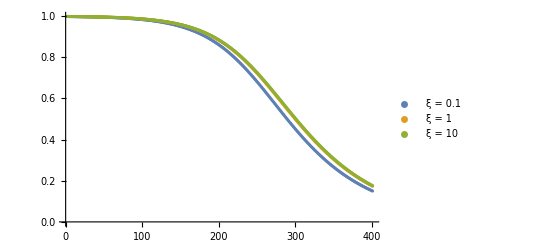

```mathematica
ListPlot[{ratioLowN1, ratioLowN2, ratioLowN3}, PlotLegends -> {"ξ = 0.1", "ξ = 1", "ξ = 10"}]
```

## Cross checking limits

```mathematica
Series[PolyGamma[0, n], {n, 0, 1}]
```

-1/n-EulerGamma+(π^2 n)/6+O[n]^2

```mathematica
Series[PolyGamma[0, n], {n, ∞, 1}]
```

Log[n]-1/(2 n)+O[1/n]^2

```mathematica
Series[Hypergeometric2F1[n - δ, 1/2, 1 - δ, α], {δ, 0, 1}]
```

Hypergeometric2F1[1/2,n,1,α]+(-Hypergeometric2F1^(0,0,1,0)[1/2,n,1,α]-Hypergeometric2F1^(0,1,0,0)[1/2,n,1,α]) δ+O[δ]^2

```mathematica
Series[Hypergeometric2F1[1/2 + δ, n, 1 + δ, α], {δ, 0, 1}]
```

Hypergeometric2F1[1/2,n,1,α]+(Hypergeometric2F1^(0,0,1,0)[n,1/2,1,α]+Hypergeometric2F1^(0,1,0,0)[n,1/2,1,α]) δ+O[δ]^2

```mathematica
Hypergeometric2F1[0, 1/2, 1, 1 - a2]
```

1

```mathematica
Hypergeometric2F1[1/2, 0, 1 , 1 - a2]
```

1

```mathematica
Series[Beta[n, 1/2], {n, 0, 1}]
```

1/n+(-EulerGamma-PolyGamma[0,1/2])+1/6 (3 EulerGamma^2-π^2+6 EulerGamma PolyGamma[0,1/2]+3 PolyGamma[0,1/2]^2) n+O[n]^2

```mathematica
Series[Beta[n, 1/2], {n, ∞, 1}]
```

√π √(1/n)+O[1/n]^(3/2)

```mathematica
Series[Log[1- α], {α, 1, 2}]
```

Log[1-α]+O[α-1]^3

## Preparing for GP approach

```mathematica
Clear[n]
Clear[ξ]
```

```mathematica
(* 2 pre factor, shift nkirill -> nmine - 1 *)
```

```mathematica
functionξ = 1/ξ Beta[n, 1/2 + δ] Hypergeometric2F1[1/2 + δ, n, n + 1/2, a2] /. a2 -> (√(ξ + 1) - √ξ)^4
```

(Beta[n,1/2] Hypergeometric2F1[1/2,n,1/2+n,(-√ξ+√(1+ξ))^4])/ξ

```mathematica
functionLowξ = -1/2 Log[ξ]/ξ - 1/ξ(PolyGamma[n] + EulerGamma)
```

-Log[ξ]/(2 ξ)-(EulerGamma+PolyGamma[0,n])/ξ

```mathematica
functionLargeξ = 1/ξ Beta[n, 1/2]
```

Beta[n,1/2]/ξ

```mathematica
n = 2;
δ = 0;
```

```mathematica
(* Table of values of logξ and dsigma/dξ at low ξ *)
(* To be exported in form of txt files for the GP *)
```

```mathematica
tableExactξ = Table[{lnξ, functionξ} /. ξ -> 10^lnξ, {lnξ, -3,1.5, 0.01}];
exactξ = tableExactξ[[All, 1]];
Export["~/Desktop/N3PDF/Tools/Cryptomancy/pt_exact.txt",%];
exactSigma = tableExactξ[[All, 2]];
Export["~/Desktop/N3PDF/Tools/Cryptomancy/sigma_exact.txt",%];
```

```mathematica
(* Table of values of logξ and dsigma/dξ at low ξ *)
(* To be exported in form of txt files for the GP *)
```

```mathematica
tableLowξ = Table[{lnξ, functionLowξ} /. ξ -> 10^lnξ, {lnξ, -3,-2, 0.1}]
Lowξ2 = tableLowξ[[All, 1]]
Export["~/Desktop/N3PDF/Tools/Cryptomancy/pt_low.txt",%];
sigmaLowξ2 = tableLowξ[[All, 2]]
Export["~/Desktop/N3PDF/Tools/Cryptomancy/sigma_low_pt.txt",%];
```

{{-3.,2453.88},{-2.9,1857.73},{-2.8,1403.01},{-2.7,1056.75},{-2.6,793.571},{-2.5,593.949},{-2.4,442.871},{-2.3,328.814},{-2.2,242.939},{-2.1,178.48},{-2.,130.259}}

{-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.}

{2453.88,1857.73,1403.01,1056.75,793.571,593.949,442.871,328.814,242.939,178.48,130.259}

```mathematica
(* Table of values of logξ and dsigma/dξ at large ξ *)
(* To be exported in form of txt files for the GP *)
```

```mathematica
tableLargeξ = Table[{lnξ, functionLargeξ} /. ξ -> 10^lnξ, {lnξ, 0.5,1.5, 0.1}]
largeξ2 = tableLargeξ[[All, 1]]
Export["~/Desktop/N3PDF/Tools/Cryptomancy/pt_large.txt",%];
sigmaLargeξ2 = tableLargeξ[[All, 2]]
Export["~/Desktop/N3PDF/Tools/Cryptomancy/sigma_large_pt.txt",%];
```

{{0.5,0.421637},{0.6,0.334918},{0.7,0.266035},{0.8,0.211319},{0.9,0.167857},{1.,0.133333},{1.1,0.10591},{1.2,0.0841276},{1.3,0.066825},{1.4,0.053081},{1.5,0.0421637}}

{0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5}

{0.421637,0.334918,0.266035,0.211319,0.167857,0.133333,0.10591,0.0841276,0.066825,0.053081,0.0421637}

```mathematica
(* Checking numbers from scypy *)
```

```mathematica
N[PolyGamma[0, 1/2]]
```

-1.96351

```mathematica
N[EulerGamma]
```

0.577216

```mathematica
-1/2 Log[0.1]/0.1 - 1/0.1(PolyGamma[n] + EulerGamma)
```

1.51293

```mathematica
1/0.1 Beta[n, 1/2]
```

13.3333